## Direct Derivation of the Dynamic Regressor for a Stanford Arm examples of the theoretical results presented in: "Explicit Lagrangian Formulation of the Dynamic Regressors for Serial Manipulators", M. Gabiccini, A. Bracci, D. De Carli, M. Fredianelli, A. Bicchi submitted to the 2009 IEEE International Conference on Robotics and Automation (ICRA2009) to be held in Kobe, Japan, May 12 - 17, 2009

### Package

```mathematica
<<ScrewCalculusPro`ScrewCalculusPro`
```

### UR10e Manipulator - definition of required quantities

Denavit-Hartenberg table with joint types added in the last slot [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tableUR10e[q1_,q2_,q3_]={
{0,            -Pi/2, 0.1273,q1,"R"},
{0.6120,    0        , 0.220941,q2,"R"},
{0.5723,    0        ,-0.1719,q3,"R"}
}
```

{{0,-π/2,0.1273,q1,R},{0.612,0,0.220941,q2,R},{0.5723,0,-0.1719,q3,R}}

Symbolic variable definition [REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
qsym={q1,q2,q3}
```

{q1,q2,q3}

List of CGi's position vectors with respect to the local D-H frames [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
CGtableUR10e=Table[ToExpression[{"a"<>ToString[i],"b"<>ToString[i],"c"<>ToString[i]}],{i,1,Length[tableUR10e@@qsym]}]
```

{{a1,b1,c1},{a2,b2,c2},{a3,b3,c3}}

List of inertia matrices with respect to the local CGi's [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
tensorlist=Table[ToExpression[{
{"I"<>ToString[i]<>"xx","-I"<>ToString[i]<>"xy","-I"<>ToString[i]<>"xz"},
{"-I"<>ToString[i]<>"xy","I"<>ToString[i]<>"yy","-I"<>ToString[i]<>"yz"},
{"-I"<>ToString[i]<>"xz","-I"<>ToString[i]<>"yz","I"<>ToString[i]<>"zz"}
}],{i,1,Length[tableUR10e@@qsym]}]
```

{{{I1xx,-I1xy,-I1xz},{-I1xy,I1yy,-I1yz},{-I1xz,-I1yz,I1zz}},{{I2xx,-I2xy,-I2xz},{-I2xy,I2yy,-I2yz},{-I2xz,-I2yz,I2zz}},{{I3xx,-I3xy,-I3xz},{-I3xy,I3yy,-I3yz},{-I3xz,-I3yz,I3zz}}}

Extract just the first...

List of link masses [NOT REQUIRED FOR DIRECT REGRESSOR CALCULATION]

```mathematica
masslist=Table[ToExpression["m"<>ToString[i]],{i,1,Length[tableUR10e@@qsym]}]
```

{m1,m2,m3}

### Time dependent variable definitions [ALL REQUIRED]

Version time dependent, configuration

```mathematica
q[t_]=Map[ToExpression[ToString[#]<>"[t]"]&,qsym]
```

{q1[t],q2[t],q3[t]}

Velocity

```mathematica
qp[t_]=D[q[t],t]
```

{q1'[t],q2'[t],q3'[t]}

Acceleration

```mathematica
qpp[t_]=D[qp[t],t]
```

{q1''[t],q2''[t],q3''[t]}

Reference velocity in the Slotine-Li algorithm

```mathematica
v[t_]=Table[ToExpression["v"<>ToString[i]<>"[t]"],{i,1,Length[tableUR10e@@qsym]}]
```

{v1[t],v2[t],v3[t]}

Its time derivative

```mathematica
vp[t_]=D[v[t],t]
```

{v1'[t],v2'[t],v3'[t]}

Gravity is defined once as

```mathematica
g0={0,0,-g}
```

{0,0,-g}

### Direct regressor calculations

```mathematica
?Regressor
```

Regressor[DHtable, q, qp, v, vp, t, g0, k] directly computes the regressor for the supplied: DHtable, q (config.), qp (velocity), v (reference velocity), vp (reference acceleration),  t (independent var),
g0 (components of gravity in {0}), k (contribute for the k-th link). If k is omitted the complete regressor is returned.

Dynamic Regressor for the first link alone

```mathematica
Y1=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,1]//FullSimplify);Y1//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1. v1'[t] | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Y1//Dimensions
```

Dynamic Regressor for the second link alone

```mathematica
Y2=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0,2]//FullSimplify);Y2//Simplify//MatrixForm
```

((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) v1[t] q2'[t]+v2[t] ((-1.38778×10^-17 Sin[2 q1[t]] Sin[q2[t]]-0.187272 Sin[2 q2[t]]) q1'[t]+0.135216 Cos[q2[t]] q2'[t])+(0.236087+0.187272 Cos[2 q2[t]]) v1'[t]+0.135216 Sin[q2[t]] v2'[t] | -0.612 Sin[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Sin[2 q2[t]] q1'[t]+0.220941 Cos[q2[t]] q2'[t])+(0.612+0.612 Cos[2 q2[t]]) v1'[t]+0.220941 Sin[q2[t]] v2'[t] | -0.612 Cos[2 q2[t]] v1[t] q2'[t]+v2[t] (-0.612 Cos[2 q2[t]] q1'[t]-0.220941 Sin[q2[t]] q2'[t])-0.612 Sin[2 q2[t]] v1'[t]+0.220941 Cos[q2[t]] v2'[t] | 0.612 Cos[q2[t]] v2[t] q2'[t]+0.441882 v1'[t]+0.612 Sin[q2[t]] v2'[t] | Sin[q2[t]] (Cos[q2[t]] (1. v2[t] q1'[t]+1. v1[t] q2'[t])+1. Sin[q2[t]] v1'[t]) | Cos[2 q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])-1. Sin[2 q2[t]] v1'[t] | 1. Cos[q2[t]] v2[t] q2'[t]+1. Sin[q2[t]] v2'[t] | Cos[q2[t]] (Sin[q2[t]] (-1. v2[t] q1'[t]-1. v1[t] q2'[t])+1. Cos[q2[t]] v1'[t]) | -1. Sin[q2[t]] v2[t] q2'[t]+1. Cos[q2[t]] v2'[t] | 0.
-0.612 g Cos[q2[t]]+0.187272 Sin[2 q2[t]] v1[t] q1'[t]+0.135216 Sin[q2[t]] v1'[t]+0.374544 v2'[t] | -1. g Cos[q2[t]]+Sin[2 q2[t]] (0.612 v1[t] q1'[t]-2.77556×10^-17 v2[t] q2'[t])+0.220941 Sin[q2[t]] v1'[t]+1.224 v2'[t] | 1. g Sin[q2[t]]+Cos[2 q2[t]] (0.612 v1[t] q1'[t]-5.55112×10^-17 v2[t] q2'[t])+0.220941 Cos[q2[t]] v1'[t] | -1.38778×10^-17 Cos[q2[t]] v2[t] q1'[t]+0.612 Sin[q2[t]] v1'[t] | -0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[2 q2[t]] v1[t] q1'[t] | 1. Sin[q2[t]] v1'[t] | 0.5 Sin[2 q2[t]] v1[t] q1'[t] | 1. Cos[q2[t]] v1'[t] | 1. v2'[t]
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Regressor for the whole manipulator

```mathematica
Y=(Regressor[tableUR10e@@q[t],q[t],qp[t],v[t],vp[t],t,g0]);
```

```mathematica
Y//Simplify
```

Structure of the Regressor for the Stanford Manipulator - the white columns show which parameters do not affect the manipulator dynamics

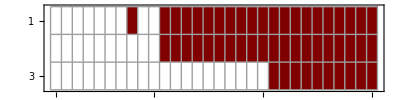

```mathematica
MatrixPlot[Y,ColorFunction->"Monochrome",AspectRatio->(1/4),Mesh-> All]
```

```mathematica
theFile=File["Yyyyy.txt"];
Export[theFile,Y//Simplify];
```

### Standard way of deriving the equations of motion

Calculation of all 6 equations of motion

```mathematica
classicaleqs=DynamicEquations[tableUR10e@@q[t],CGtableUR10e,masslist,tensorlist,g0,q[t],qp[t],v[t],vp[t]];
```

We show just the first one...

```mathematica
classicaleqs[[1]];
```

### Equations of motion obtained multiplying the Dynamic Regressor and the List of Dynamic Parameters

Contestualmente alla creazione della lista di parametri (10 per ciascun link) i momenti di inerzia vengono scritti rispetto all'origine del frame di DH ancora in componenti nel frame di DH.

As we create the complete list with masses, first moments of inertia and second moments of inertia, we calculate the moments of inertia with respect to the local D-H frames, as indicated in the paper

```mathematica
paramlist=ExtractParameters[CGtableUR10e,masslist,tensorlist]//Simplify;paramlist
```

{m1,a1 m1,b1 m1,c1 m1,I1xx+(b1^2+c1^2) m1,I1xy+a1 b1 m1,I1xz+a1 c1 m1,I1yy+(a1^2+c1^2) m1,I1yz+b1 c1 m1,I1zz+(a1^2+b1^2) m1,m2,a2 m2,b2 m2,c2 m2,I2xx+(b2^2+c2^2) m2,I2xy+a2 b2 m2,I2xz+a2 c2 m2,I2yy+(a2^2+c2^2) m2,I2yz+b2 c2 m2,I2zz+(a2^2+b2^2) m2,m3,a3 m3,b3 m3,c3 m3,I3xx+(b3^2+c3^2) m3,I3xy+a3 b3 m3,I3xz+a3 c3 m3,I3yy+(a3^2+c3^2) m3,I3yz+b3 c3 m3,I3zz+(a3^2+b3^2) m3}

Extract just the parameters for the first link...

```mathematica
paramlist[[1;;10]]
```

Equations of motion with the regressor

```mathematica
regressoreqs=Y.paramlist;
```

### A little detour inside the package (just to show other useful functions)

Computation of the forward kinematics for the defined Denavit-Hartenberg table

```mathematica
FK= DHFKine[tableUR10e@@qsym]//FullSimplify
FK//Dimensions
```

{{Cos[q1] Cos[q2+q3],-Cos[q1] Sin[q2+q3],-1. Sin[q1],Cos[q1] (0.612 Cos[q2]+0.5723 Cos[q2+q3])-0.049041 Sin[q1]},{Cos[q2+q3] Sin[q1],-Sin[q1] Sin[q2+q3],1. Cos[q1],0.049041 Cos[q1]+(0.612 Cos[q2]+0.5723 Cos[q2+q3]) Sin[q1]},{-1. Sin[q2+q3],-1. Cos[q2+q3],0.,0.1273-0.612 Sin[q2]-0.5723 Sin[q2+q3]},{0.,0.,0.,1.}}

{4,4}

```mathematica
theFile=File["FK.txt"];
```

```mathematica
Export[theFile,FK];
```

Full Jacobian (classical for differntial kinematics)

```mathematica
JJ=DHJacob0[tableUR10e@@qsym]//FullSimplify
```

```mathematica
theFile=File["JJ.txt"];
Export[theFile,JJ];
```

```mathematica
D[JJ[q1_,q2_,q3_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify
```

{{Cos[q1[t]] (-0.612 Cos[q2[t]]-0.5723 Cos[q2[t]+q3[t]]) q1'[t]+0.049041 Sin[q1[t]] q1'[t]+Sin[q1[t]] (0.612 Sin[q2[t]] q2'[t]+0.5723 Sin[q2[t]+q3[t]] (q2'[t]+q3'[t])),Sin[q1[t]] (0.612 Sin[q2[t]]+0.5723 Sin[q2[t]+q3[t]]) q1'[t]+Cos[q1[t]] (-0.612 Cos[q2[t]] q2'[t]-0.5723 Cos[q2[t]+q3[t]] (q2'[t]+q3'[t])),0.5723 Sin[q1[t]] Sin[q2[t]+q3[t]] q1'[t]-0.5723 Cos[q1[t]] Cos[q2[t]+q3[t]] (q2'[t]+q3'[t])},{-0.049041 Cos[q1[t]] q1'[t]+(-0.612 Cos[q2[t]]-0.5723 Cos[q2[t]+q3[t]]) Sin[q1[t]] q1'[t]+Cos[q1[t]] (-0.612 Sin[q2[t]] q2'[t]-0.5723 Sin[q2[t]+q3[t]] (q2'[t]+q3'[t])),Cos[q1[t]] (-0.612 Sin[q2[t]]-0.5723 Sin[q2[t]+q3[t]]) q1'[t]+Sin[q1[t]] (-0.612 Cos[q2[t]] q2'[t]-0.5723 Cos[q2[t]+q3[t]] (q2'[t]+q3'[t])),-0.5723 Cos[q1[t]] Sin[q2[t]+q3[t]] q1'[t]-0.5723 Cos[q2[t]+q3[t]] Sin[q1[t]] (q2'[t]+q3'[t])},{0,0.612 Sin[q2[t]] q2'[t]+0.5723 Sin[q2[t]+q3[t]] (q2'[t]+q3'[t]),0.5723 Sin[q2[t]+q3[t]] (q2'[t]+q3'[t])},{0,-Cos[q1[t]] q1'[t],-1. Cos[q1[t]] q1'[t]},{0,-Sin[q1[t]] q1'[t],-1. Sin[q1[t]] q1'[t]},{0,0,0}}

Derivata del jacobiano

```mathematica
theFile=File["DJJ.txt"];
Export[theFile,D[JJ[q1_,q2_,q3_,q4_,q5_,q6_]=DHJacob0[tableUR10e@@q[t]]//FullSimplify,t]//FullSimplify];
```

Partial Jacobians (version for regressor dynamics) - reference points are still the origins of DH frames

For the first link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,1]//FullSimplify
```

For the second link

```mathematica
DHJacob0Dyn[tableUR10e@@qsym,2]//FullSimplify
```

Partial Jacobians (version for classical dynamics) - reference points are now the CGs of the link - a separate list must be supplied

First link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,1]
```

Third link

```mathematica
CGJacob0Dyn[tableUR10e@@qsym,CGtableUR10e,3]
```

Inertia matrix

```mathematica
Bmat[q1_,q2_,q3_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify
```

{{1. I1yy+0.5 I3xx+0.5 I3yy+(a1^2+c1^2) m1-0.5 I3xx Cos[2 (q2+q3)]+0.5 I3yy Cos[2 (q2+q3)]+Sin[q2] (-1. I2xy Cos[q2]+1. I2xx Sin[q2])+Cos[q2] (1. I2yy Cos[q2]-1. I2xy Sin[q2])+m2 (((-0.220941-1. c2) Sin[q1]+Cos[q1] ((0.612+a2) Cos[q2]-1. b2 Sin[q2]))^2+((-0.220941-1. c2) Cos[q1]+Sin[q1] (-1. (0.612+a2) Cos[q2]+b2 Sin[q2]))^2)+m3 (((-0.049041-1. c3) Sin[q1]+Cos[q1] (Sin[q2] (-1. b3 Cos[q3]+(-0.5723-1. a3) Sin[q3])+Cos[q2] (0.612+(0.5723+a3) Cos[q3]-1. b3 Sin[q3])))^2+1. ((0.049041+1. c3) Cos[q1]+Sin[q1] (0.612 Cos[q2]+(0.5723+1. a3) Cos[q2+q3]-1. b3 Sin[q2+q3]))^2)-1. I3xy Sin[2 (q2+q3)],(1. I2yz+b2 (0.220941+1. c2) m2) Cos[q2]+(1. I3yz+b3 (0.049041+1. c3) m3) Cos[q2+q3]+1. I2xz Sin[q2]+0.135216 m2 Sin[q2]+0.220941 a2 m2 Sin[q2]+0.612 c2 m2 Sin[q2]+1. a2 c2 m2 Sin[q2]+0.0300131 m3 Sin[q2]+0.612 c3 m3 Sin[q2]+1. I3xz Sin[q2+q3]+0.0280662 m3 Sin[q2+q3]+0.049041 a3 m3 Sin[q2+q3]+0.5723 c3 m3 Sin[q2+q3]+1. a3 c3 m3 Sin[q2+q3],(1. I3yz+b3 (0.049041+1. c3) m3) Cos[q2+q3]+(1. I3xz+(0.0280662+0.049041 a3+0.5723 c3+1. a3 c3) m3) Sin[q2+q3]},{(1. I2yz+b2 (0.220941+1. c2) m2) Cos[q2]+(1. I3yz+b3 (0.049041+1. c3) m3) Cos[q2+q3]+1. I2xz Sin[q2]+0.135216 m2 Sin[q2]+0.220941 a2 m2 Sin[q2]+0.612 c2 m2 Sin[q2]+1. a2 c2 m2 Sin[q2]+0.0300131 m3 Sin[q2]+0.612 c3 m3 Sin[q2]+1. I3xz Sin[q2+q3]+0.0280662 m3 Sin[q2+q3]+0.049041 a3 m3 Sin[q2+q3]+0.5723 c3 m3 Sin[q2+q3]+1. a3 c3 m3 Sin[q2+q3],1. I2zz+1. I3zz+0.374544 m2+1.224 a2 m2+1. a2^2 m2+1. b2^2 m2+0.702071 m3+1.1446 a3 m3+1. a3^2 m3+1. b3^2 m3+(0.700495+1.224 a3) m3 Cos[q3]-1.224 b3 m3 Sin[q3],1. I3zz+0.327527 m3+1.1446 a3 m3+1. a3^2 m3+1. b3^2 m3+(0.350248+0.612 a3) m3 Cos[q3]-0.612 b3 m3 Sin[q3]},{(1. I3yz+b3 (0.049041+1. c3) m3) Cos[q2+q3]+(1. I3xz+(0.0280662+0.049041 a3+0.5723 c3+1. a3 c3) m3) Sin[q2+q3],1. I3zz+0.327527 m3+1.1446 a3 m3+1. a3^2 m3+1. b3^2 m3+(0.350248+0.612 a3) m3 Cos[q3]-0.612 b3 m3 Sin[q3],(0.+0. ⅈ)+(1.+0. ⅈ) I3zz+((0.327527+0. ⅈ)+(1.1446+0. ⅈ) a3+(1.+0. ⅈ) a3^2+(1.+0. ⅈ) b3^2) m3}}

```mathematica
theFile=File["B_3r.txt"];
Export[theFile,Bmat[q1_,q2_,q3_,q4_,q5_,q6_]=Inertia[tableUR10e@@qsym,CGtableUR10e,masslist,tensorlist]//Simplify];
```

We map it of the time dependent joint vector

```mathematica
Bmat@@qsym
```

We check its symmetry!

```mathematica
Bmat@@qsym
```

```mathematica
(*Bmat@@qsym-Transpose[Bmat@@qsym]//Simplify*)
```

We compute the Coriolis matrix derived from the Christoffel symbols

```mathematica
Cmat=InertiaToCoriolis[Bmat@@q[t],q[t],qp[t]];
```

```mathematica
Cmat[1]
```

```mathematica
Cmat = Simplify[Cmat,TimeConstraint->0.1]//Timing
```

```mathematica
Cmat=Cmat//Chop
```

```mathematica
Cmat = Cmat//Simplify
```

```mathematica
theFile=File["C_3r.txt"];
Export[theFile,Cmat//Simplify];
```

```mathematica
Gvec=Gravitational[tableUR10e@@qsym,CGtableUR10e,masslist,g0]//FullSimplify
```

{0.,-1. g (((0.612+1. a2) m2+0.612 m3) Cos[q2]+(0.5723+1. a3) m3 Cos[q2+q3]-1. b2 m2 Sin[q2]-1. b3 m3 Sin[q2+q3]),g m3 ((-0.5723-1. a3) Cos[q2+q3]+1. b3 Sin[q2+q3])}

```mathematica
theFile=File["G_3r.txt"];
Export[theFile,Gvec];
```